## Thermodynamic quantities: Condensate Ansatz

## Ideal Gas limits

```mathematica
Nc=2;Nf=2;
Pideal=π^2/45 T^4(Nc^2-1)+(7 π^2)/180 T^4 Nc Nf;
Eideal=π^2/15 T^4(Nc^2-1)+(7 π^2)/60 T^4 Nc Nf;
Sideal=4 π^2/45 T^3(Nc^2-1+7/4 Nc Nf);
```

```mathematica
Pideal
```

(2 π^2 T^4)/9

```mathematica
Eideal
```

(19 π^2 T^4)/12

```mathematica
Sideal
```

(19 π^2 T^3)/9

```mathematica
91200/Exp[(6π)/(23(0.1184))]//N
```

89.9244

## Normalised Plots

```mathematica
(*Press=pressure,Sden=entropy density, Eden =energy density*)
```

```mathematica
Λms=200;
```

```mathematica
Clear[c1,c2,Λ,β0,T,Λms]
Λ= T;Nc=2;Nf=2;β0=1/(4π)^2(11/3 Nc-2/3 Nf);
α[T_]=2Log[Λ/Λms];
αs[T_]=1/(4π β0 α[T])(1);(*For only loop *)
Press[c1_,c2_,T_,Λms_]= -(-1/45 (-1+Nc^2) π^2 (T)^4-7/180 Nc Nf π^2 (T)^4-1/(48 π^2)c1^3 (-Nc+Nf) (2 c1-ⅈ T JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+ⅈ T JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1])-2 c1^3 (c1-2 ⅈ T JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+2 ⅈ T JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1]) (-(1/(4 (4π) αs[T]))-(Nf Log[4])/(48 π^2)+1/2 β0 Log[Λ/(4 π T)]));
Thdpot[c1_,c2_,T_,Λms_]= (-1/45 (-1+Nc^2) π^2 (T)^4-7/180 Nc Nf π^2 (T)^4-1/(48 π^2)c1^3 (-Nc+Nf) (2 c1-ⅈ T JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+ⅈ T JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1])-2 c1^3 (c1-2 ⅈ T JacobiCN[c1 c2,-1] JacobiDN[c1 c2,-1] JacobiSN[c1 c2,-1]+2 ⅈ T JacobiCN[c1 (c2-ⅈ/T),-1] JacobiDN[c1 (c2-ⅈ/T),-1] JacobiSN[c1 (c2-ⅈ/T),-1]) (-(1/(4 (4π) αs[T]))-(Nf Log[4])/(48 π^2)+1/2 β0 Log[Λ/(4 π T)]));
```

```mathematica
Sden[c1_,c2_,T_,Λms_]=-D[Thdpot[c1,c2,T,Λms],T];
```

```mathematica
Enden[c1_,c2_,T_,Λms_]= -Press[c1,c2,T,Λms]+ T Sden[c1,c2,T,Λms];
```

```mathematica
Press1[c1_,c2_,T_,Λms_]=Press[c1,c2,T,Λms]/Pideal;
Thdpot1[c1_,c2_,T_,Λms_]=Thdpot[c1,c2,T,Λms]/Pideal;
Sden1[c1_,c2_,T_,Λms_]=Sden[c1,c2,T,Λms]/Sideal;
Enden1[c1_,c2_,T_,Λms_]=Enden[c1,c2,T,Λms]/Eideal;
```

### Case A: Condensate is not in equilibrium with quantum fluctuations

```mathematica
(*For c2=0 and for c2 << β *)
```

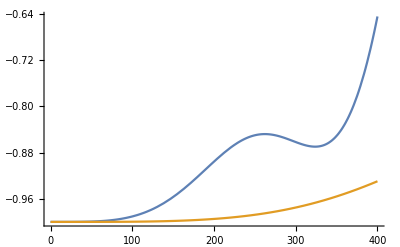

```mathematica
Plot[{Thdpot1[c1,0,200],Thdpot1[c1,0,500]},{c1,0,400}]
```

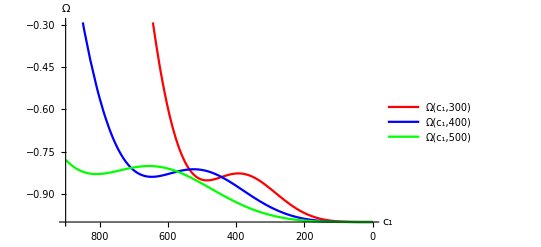

```mathematica
Plot[{Thdpot1[c1,0,300],Thdpot1[c1,0,400],Thdpot1[c1,0,500]},{c1,900,0},AxesOrigin->{900,-1},PlotStyle->{Red,Blue,Green},AxesLabel->{"c_1","Ω"},PlotLegends->Placed[{"Ω(c_1,300)","Ω(c_1,400)","Ω(c_1,500)"},{Scaled[{0.5,0.9}], {0, 0.8}}],ScalingFunctions->{"Reverse",Automatic}]
```

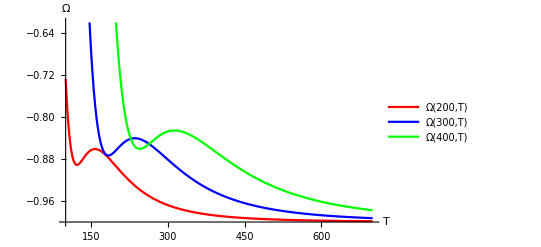

```mathematica
Plot[{Thdpot1[200,0,T],Thdpot1[300,0,T],Thdpot1[400,0,T]},{T,100,700},AxesOrigin->{100,-1},PlotStyle->{Red,Blue,Green},AxesLabel->{"T","Ω"},PlotLegends->Placed[{"Ω(200,T)","Ω(300,T)","Ω(400,T)"},{Right,Center}]]
```

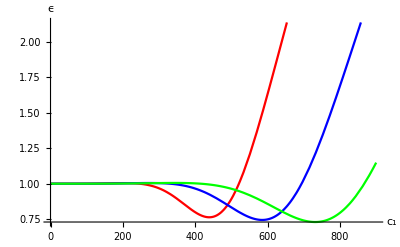

```mathematica
Plot[{Enden1[c1,0,300],Enden1[c1,0,400],Enden1[c1,0,500]},{c1,900,0},PlotStyle->{Red,Blue,Green},AxesLabel->{"c_1","ϵ"}]
```

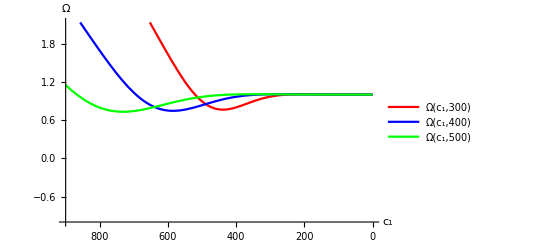

```mathematica
Plot[{Enden1[c1,0,300],Enden1[c1,0,400],Enden1[c1,0,500]},{c1,900,0},AxesOrigin->{900,-1},PlotStyle->{Red,Blue,Green},AxesLabel->{"c_1","Ω"},PlotLegends->Placed[{"Ω(c_1,300)","Ω(c_1,400)","Ω(c_1,500)"},{Scaled[{0.5,0.9}], {0, 0.8}}],ScalingFunctions->{"Reverse",Automatic}]
```

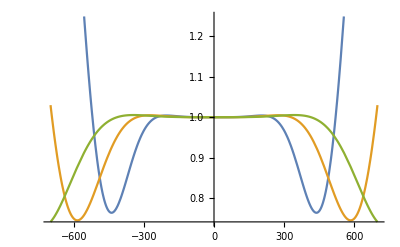

```mathematica
Plot[{Enden1[c1,0,300],Enden1[c1,0,400],Enden1[c1,0,500]},{c1,-700,700}]
```

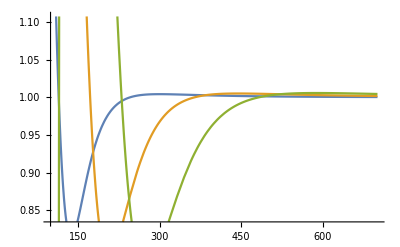

```mathematica
Plot[{Enden1[200,0,T],Enden1[300,0,T],Enden1[400,0,T]},{T,100,700}]
```

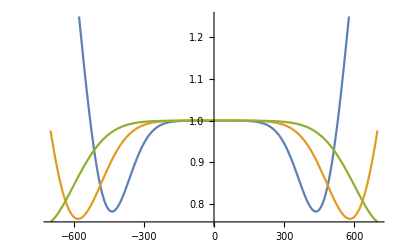

```mathematica
Plot[{Sden1[c1,0,300],Sden1[c1,0,400],Sden1[c1,0,500]},{c1,-700,700}]
```

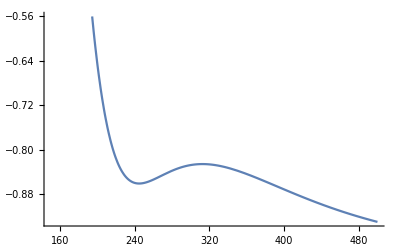

```mathematica
Plot[Thdpot1[400,0,T],{T,150,500}]
```

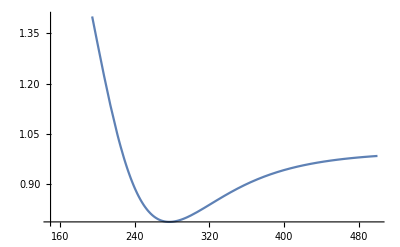

```mathematica
Plot[Sden1[400,0,T],{T,150,500}]
```

```mathematica
(*For c2 \neq 0*)
```

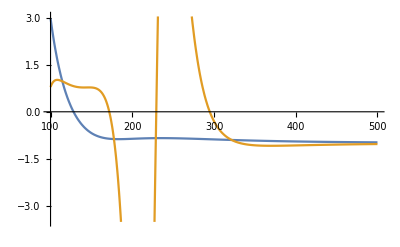

```mathematica
Plot[{Thdpot1[300,0,T],Re[Thdpot1[300,1,T]]},{T,100,500}]
```

```mathematica
Table[Thdpot1[300,c2,300],{c2,0,10,0.5}]
```

{-0.881468+0. ⅈ,-0.744993-0.125965 ⅈ,-0.302571+1.91826 ⅈ,0.0353981-0.861352 ⅈ,-0.799456+0.10913 ⅈ,-0.878948-0.0218379 ⅈ,-0.66153-0.129674 ⅈ,-1.9656+2.79818 ⅈ,-0.133509-0.260977 ⅈ,-0.834916+0.0876224 ⅈ,-0.871009-0.0439839 ⅈ,-0.534761-0.100488 ⅈ,-4.40205+1.48805 ⅈ,-0.365179+0.00500471 ⅈ,-0.857731+0.0649428 ⅈ,-0.856431-0.0665611 ⅈ,-0.349987+0.00688936 ⅈ,-4.27307-1.68171 ⅈ,-0.545567+0.104398 ⅈ,-0.871774+0.0423926 ⅈ,-0.832868-0.0892172 ⅈ}

### Case B: Condensate is in equilibrium with quantum fluctuations

All thermodynamics are only a function of Temperature.

```mathematica
(* c1 -> 4 I EllipticK[-1] T *)
```

```mathematica
Sden2[T_,c2_,Λms_]=-D[Thdpot[4 I EllipticK[-1] T ,c2,T,Λms],T];
```

```mathematica
Sden22[T_,c2_,Λms_]=Sden2[T,c2,Λms]/Sideal;
```

```mathematica
Enden2[T_,c2_,Λms_]= -Press[4I EllipticK[-1] T,c2,T,Λms]+ T Sden2[T,c2,Λms];
```

```mathematica
Enden22[T_,c2_,Λms_]=Enden2[T,c2,Λms]/Eideal;
```

```mathematica
(*Normalised pressure*)
```

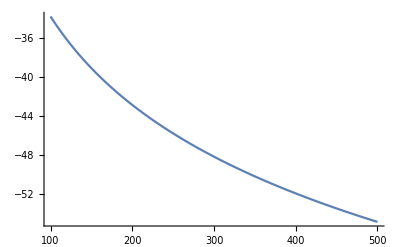

```mathematica
Plot[Press1[4I EllipticK[-1] T,0,T,120],{T,100,500}]
```

```mathematica
(*Normalised energy density*)
```

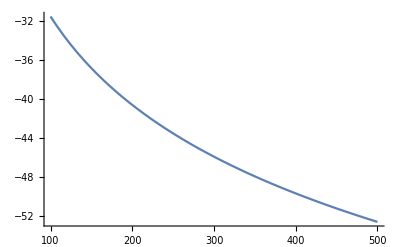

```mathematica
Plot[Enden22[T,0,200],{T,100,500}]
```

```mathematica
(*w=Pressure/energydensity*)
```

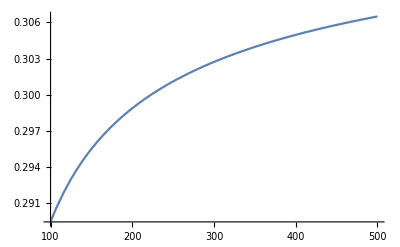

```mathematica
Plot[Press[4I EllipticK[-1] T,0,T,176]/Enden2[T,0,176],{T,100,500}]
```

```mathematica
(*ideal gas: w=pressure/energydensity*)
```

```mathematica
Pideal/Eideal
```

1/3

## Thermodynamic quantities: Condensate Ansatz + GW

## Case A: Not in equilibrium

```mathematica
Clear[c1,c2,Ap,ωg,t,u,hp]
```

```mathematica
u[t_]=c1 JacobiSN[c1(-I t+c2),-1]
```

c1 JacobiSN[c1 (c2-ⅈ t),-1]

```mathematica
hp[t_]=Ap Cos[ ωg (-I t)]
```

Ap Cosh[t ωg]

```mathematica
(*F^2 term*)
```

```mathematica
6 D[u[t],t]^2 +6 u[t]^4+1/8 hp[t]^4 u[t]^4+hp[t]^2 D[u[t],t]^2+2 hp[t]u[t]u'[t]hp'[t]+u[t]^2 hp'[t]^2
```

-6 c1^4 JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2-Ap^2 c1^4 Cosh[t ωg]^2 JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2+6 c1^4 JacobiSN[c1 (c2-ⅈ t),-1]^4+1/8 Ap^4 c1^4 Cosh[t ωg]^4 JacobiSN[c1 (c2-ⅈ t),-1]^4-2 ⅈ Ap^2 c1^3 ωg Cosh[t ωg] JacobiCN[c1 (c2-ⅈ t),-1] JacobiDN[c1 (c2-ⅈ t),-1] JacobiSN[c1 (c2-ⅈ t),-1] Sinh[t ωg]+Ap^2 c1^2 ωg^2 JacobiSN[c1 (c2-ⅈ t),-1]^2 Sinh[t ωg]^2

```mathematica
Clear[I1,I2]
```

```mathematica
I1[T_?NumberQ]:=NIntegrate[-6 c1^4 JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2-Ap^2 c1^4 Cosh[t ωg]^2 JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2+6 c1^4 JacobiSN[c1 (c2-ⅈ t),-1]^4+1/8 Ap^4 c1^4 Cosh[t ωg]^4 JacobiSN[c1 (c2-ⅈ t),-1]^4-2 ⅈ Ap^2 c1^3 ωg Cosh[t ωg] JacobiCN[c1 (c2-ⅈ t),-1] JacobiDN[c1 (c2-ⅈ t),-1] JacobiSN[c1 (c2-ⅈ t),-1] Sinh[t ωg]+Ap^2 c1^2 ωg^2 JacobiSN[c1 (c2-ⅈ t),-1]^2 Sinh[t ωg]^2,{t,0,1/T}];
```

```mathematica
(*E^2 term*)
```

```mathematica
3 D[u[t],t]^2+1/2 hp[t]^2 u'[t]^2+hp[t]u[t]u'[t]hp'[t]+1/2 u[t]^2 hp'[t]^2//Simplify
```

-1/4 c1^2 (c1^2 (12+Ap^2+Ap^2 Cosh[2 t ωg]) JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2-2 Ap^2 ωg^2 JacobiSN[c1 (c2-ⅈ t),-1]^2 Sinh[t ωg]^2+2 ⅈ Ap^2 c1 ωg JacobiCN[c1 (c2-ⅈ t),-1] JacobiDN[c1 (c2-ⅈ t),-1] JacobiSN[c1 (c2-ⅈ t),-1] Sinh[2 t ωg])

```mathematica
I2[T_?NumberQ]:=NIntegrate[-1/4 c1^2 (c1^2 (12+Ap^2+Ap^2 Cosh[2 t ωg]) JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2-2 Ap^2 ωg^2 JacobiSN[c1 (c2-ⅈ t),-1]^2 Sinh[t ωg]^2+2 ⅈ Ap^2 c1 ωg JacobiCN[c1 (c2-ⅈ t),-1] JacobiDN[c1 (c2-ⅈ t),-1] JacobiSN[c1 (c2-ⅈ t),-1] Sinh[2 t ωg]),{t,0,1/T}];
```

```mathematica
c1=300;c2=0;ωg=1;Ap=0.001;
```

```mathematica
I1[300]
```

-1.09559×10^8+0. ⅈ

Thermodynamic Potential

```mathematica
Λms=176;Λ=2 π T;β0=1/(4π)^2(11/3 Nc-2/3 Nf);
α[T_]=2Log[Λ/Λms];
αs[T_]=1/(4π β0 α[T])(1);(*For only loop *)
```

```mathematica
Thdpotgw[T_]:=-((π^2/45)T^4 (Nc^2-1)+7 (π^2/180)T^4 Nc Nf -((-1)/(4 (4π)αs[T])+(1/2)β0 Log[Λ/(4π T)]-(1/(4π)^2)(Nf/3)Log[4])I1[T]-(1/3)(1/(4π)^2)(Nf-Nc)I2[T]);
```

```mathematica
Pgw[T_]=-Thdpotgw[T];
```

```mathematica
Sdengw[T_]=-D[Thdpotgw[T],T];
```

```mathematica
Endengw[T_]= -Pgw[T]+ T Sdengw[T];
```

```mathematica
Pgwn[T_]=Pgw[T]/Pideal;
Thdpotgwn[T_]=Thdpotgw[T]/Pideal;
Sdengwn[T_]=Sdengw[T]/Sideal;
Endengwn[T_]=Endengw[T]/Eideal;
```

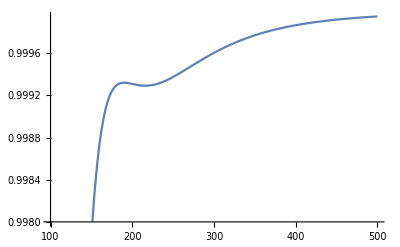

```mathematica
Plot[Re[Pgwn[T]],{T,100,500}]
```

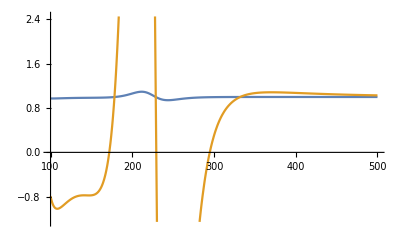

```mathematica
Plot[{Re[Pgw[T]],Re[Press1[300,1,T]]},{T,100,500}]
```

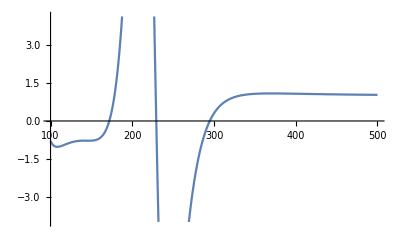

```mathematica
p2=Plot[Re[Press1[300,1,T]],{T,100,500}]
```

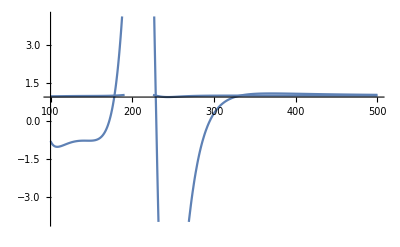

```mathematica
Show[{p1,p2},PlotRange->All]
```

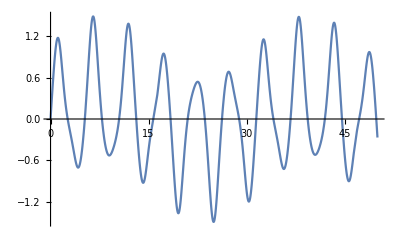

```mathematica
Plot[(1+1/2 Cos[t])JacobiSN[t,-1],{t,0,50}]
```

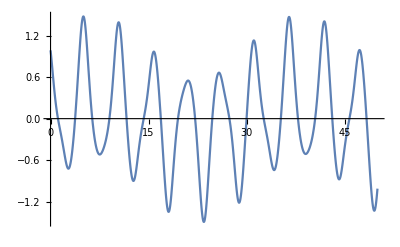

```mathematica
Plot[(1+1/2 Cos[t+2π 4EllipticK[-1]])JacobiSN[t+2π 4EllipticK[-1],-1],{t,0,50}]
```

```mathematica
4 EllipticK[-1]//N
```

5.24412

## Case B: Everything is in equilibrium

```mathematica
Clear[c1,c2,Ap,ωg,t,u]
```

```mathematica
(*c1 = 4iK(-1) T, Subscript[ω, g] = 2πiT *)
```

```mathematica
u1[t_,T_]=(4I EllipticK[-1] T) JacobiSN[(4I EllipticK[-1] T)(-I t+c2),-1]
```

4 ⅈ T EllipticK[-1] JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]

```mathematica
hp1[t_,T_]=Ap Cos[ 2π I T (-I t)]
```

Ap Cos[2 π t T]

```mathematica
(*F^2 term*)
```

```mathematica
6 D[u1[t,T],t]^2 +6 u1[t,T]^4+(1/8)hp1[t,T]^4 u[t,T]^4+hp1[t,T]^2 D[u1[t,T],t]^2+2 hp1[t,T]u1[t,T]D[u1[t,T],t]D[hp1[t,T],t]+u1[t,T]^2 D[hp1[t,T],t]^2
```

-1536 T^4 EllipticK[-1]^4 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2-256 Ap^2 T^4 Cos[2 π t T]^2 EllipticK[-1]^4 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2+1536 T^4 EllipticK[-1]^4 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^4+256 Ap^2 π T^4 Cos[2 π t T] EllipticK[-1]^3 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] Sin[2 π t T]-64 Ap^2 π^2 T^4 EllipticK[-1]^2 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 Sin[2 π t T]^2+1/8 Ap^4 Cos[2 π t T]^4 u[t,T]^4

```mathematica
I11[T_?NumberQ]:=NIntegrate[-1536 T^4 EllipticK[-1]^4 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2-256 Ap^2 T^4 Cos[2 π t T]^2 EllipticK[-1]^4 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2+1536 T^4 EllipticK[-1]^4 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^4+32 Ap^4 T^4 Cos[2 π t T]^4 EllipticK[-1]^4 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^4+256 Ap^2 π T^4 Cos[2 π t T] EllipticK[-1]^3 JacobiCN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] JacobiDN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1] Sin[2 π t T]-64 Ap^2 π^2 T^4 EllipticK[-1]^2 JacobiSN[4 ⅈ (c2-ⅈ t) T EllipticK[-1],-1]^2 Sin[2 π t T]^2,{t,0,1/T}];
```

```mathematica
(*E^2 term*)
```

```mathematica
3 D[u[t],t]^2+1/2 hp[t]^2 u'[t]^2+hp[t]u[t]u'[t]hp'[t]+1/2 u[t]^2 hp'[t]^2//Simplify
```

-1/4 c1^2 (c1^2 (12+Ap^2+Ap^2 Cosh[2 t ωg]) JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2-2 Ap^2 ωg^2 JacobiSN[c1 (c2-ⅈ t),-1]^2 Sinh[t ωg]^2+2 ⅈ Ap^2 c1 ωg JacobiCN[c1 (c2-ⅈ t),-1] JacobiDN[c1 (c2-ⅈ t),-1] JacobiSN[c1 (c2-ⅈ t),-1] Sinh[2 t ωg])

```mathematica
I2[T_?NumberQ]:=NIntegrate[-1/4 c1^2 (c1^2 (12+Ap^2+Ap^2 Cosh[2 t ωg]) JacobiCN[c1 (c2-ⅈ t),-1]^2 JacobiDN[c1 (c2-ⅈ t),-1]^2-2 Ap^2 ωg^2 JacobiSN[c1 (c2-ⅈ t),-1]^2 Sinh[t ωg]^2+2 ⅈ Ap^2 c1 ωg JacobiCN[c1 (c2-ⅈ t),-1] JacobiDN[c1 (c2-ⅈ t),-1] JacobiSN[c1 (c2-ⅈ t),-1] Sinh[2 t ωg]),{t,0,1/T}];
```

```mathematica
(*Choosing c2 and Ap*)
```

```mathematica
c2=0;Ap=0.001;
```

Thermodynamic Potential

```mathematica
Λms=176;Λ=2 π T;β0=(1/(4π)^2)((11/3)Nc-(2/3)Nf);
α[T_]=2Log[Λ/Λms];
αs[T_]=(1/(4π β0 α[T]))(1);(*For only loop *)
```

```mathematica
Thdpotgw1[T_]:=-((π^2/45)T^4 (Nc^2-1)+7 (π^2/180)T^4 Nc Nf -((-1)/(4 (4π)αs[T])+(1/2)β0 Log[Λ/(4π T)]-(1/(4π)^2)(Nf/3)Log[4])I11[T]-(1/3)(1/(4π)^2)(Nf-Nc)0);
```

```mathematica
Pgw1[T_]=-Thdpotgw1[T];
Sdengw1[T_]=-D[Thdpotgw1[T],T];
Endengw1[T_]= -Pgw1[T]+ T Sdengw1[T];
```

```mathematica
Pgw1n[T_]=Pgw1[T]/Pideal;
Thdpotgw1n[T_]=Thdpotgw1[T]/Pideal;
Sdengw1n[T_]=Sdengw1[T]/Sideal;
Endengw1n[T_]=Endengw1[T]/Eideal;
```

```mathematica
(*Normalised pressure*)
```

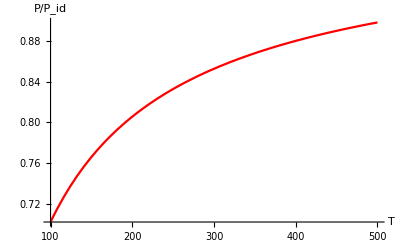

```mathematica
Plot[Re[Pgw1n[T]],{T,100,500},AxesLabel->{"T","P/P_id"},PlotStyle->Red]
```

```mathematica
(*normalised Energy density*)
```

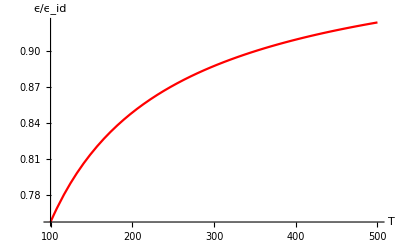

```mathematica
Plot[Re[Endengw1n[T]],{T,100,500},AxesLabel->{"T","ϵ/ϵ_id"},PlotStyle->Red]
```